Getting Started with MagneticTB

To construct a tight-binding model, first specify the lattice, atomic positions, symmetry operations, and local orbitals. With these inputs, MagneticTB finds the equivalent atoms and the symmetry-allowed hopping terms. We use graphene to show how to obtain the Hamiltonian and plot its bands.

Install, update, uninstall, and load

Obtain a local MagneticTB .paclet file, either supplied to you or built from the source. The installation commands below use this file; they do not download a release from the Internet.

### Install

MagneticTB help home

Install the .paclet file with the following command. Replace the path and filename with those of your file:

```mathematica
PacletInstall["/absolute/path/MagneticTB-2.x.y.paclet"]
```

After installation, quit Mathematica completely and open it again before loading MagneticTB or opening its help. This also removes any definitions left by the previously loaded version.

### Update

MagneticTB help home

To update, install the newer .paclet file in the same way, then quit and reopen Mathematica. If PacletInstall reports samevers, that version is already installed. To replace it with another file of the same version, uninstall that version first and then install the new file.

```mathematica
PacletInstall["/absolute/path/MagneticTB-2.x.y.paclet"]
```

### Uninstall or reinstall the same version

MagneticTB help home

To uninstall MagneticTB, run the following command, then quit and reopen Mathematica:

```mathematica
PacletUninstall["MagneticTB"]
```

### Load and open the documentation

MagneticTB help home

After reopening Mathematica, load the package with Needs. To open the help, search for MagneticTB in the Documentation Center, or run the command below to open its home page. The functions from version 1.0 are loaded with MagneticTBOld`; use a separate kernel for that version.

```mathematica
Needs["MagneticTB`"]
```

```mathematica
SystemOpen["paclet:MagneticTB/guide/MagneticTB"]
```

The five physical inputs

init sets up the crystal and its local orbitals. Here lattice gives the three lattice vectors as rows, and lattpar supplies their parameter values. wyckoffposition gives one representative position and its magnetic moment for each inequivalent Wyckoff orbit. symminformation gives the symmetry operations, and basisFunctions lists the orbitals in the same order as the positions.

The two carbon atoms in graphene are symmetry equivalent. Enter only {1/3,2/3,0}; the other atom at {2/3,1/3,0} is generated by symmetry. Keep one pz orbital on each carbon. The lattice parameter c separates the periodically repeated graphene layers.

| lattice | length | Three primitive vectors stored as rows. Coordinates in wyckoffposition are fractional coordinates in this basis.
       | lattpar | length | Numerical assignments for every symbolic lattice constant. MagneticTB does not impose an angstrom unit; all lengths must use one consistent unit.
       | wyckoffposition | fractional position and magnetic moment | The outer list enumerates inequivalent Wyckoff orbits. Each entry is {seed position, magnetic moment}; the same outer order is used by basisFunctions.
       | symminformation | symmetry operations | Each magnetic-group record is {label,R,t,"F"|"T"}. The last field records whether the operation is unitary or antiunitary.
       | basisFunctions | local orbital basis | One nonempty local basis list per Wyckoff orbit. Different entries may have different dimensions, which produces rectangular inter-orbit hopping blocks.

```mathematica
grapheneOperations = msgop[gray[191]];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 3},
  wyckoffposition -> {
    {{1/3, 2/3, 0}, {0, 0, 0}}
  },
  symminformation -> grapheneOperations,
  basisFunctions -> {{"pz"}}
];
```

View atomic positions and magnetization directions

After init, use atompos to view the generated atomic positions and magnetization directions. The atoms are grouped by Wyckoff orbit. Each entry is {fractional position, magnetization direction}, with both vectors expressed in the lattice-vector basis:

```mathematica
atompos
```

{{{{1/3,2/3,0},{0,0,0}},{{2/3,1/3,0},{0,0,0}}}}

The two entries are the carbon atoms at {1/3,2/3,0} and {2/3,1/3,0}. Their magnetization directions are both {0,0,0}, since this model is nonmagnetic.

Check the neighbour shells

Hoppings are numbered by distance. Number 1 is the onsite term, number 2 is the nearest neighbor, and number 3 is the second neighbor. For graphene, showbonds[2] displays the three nearest-neighbor carbon-carbon bonds and their reverse directions. No hopping parameters need to be specified to draw these bonds.

```mathematica
showbonds[2]
```

Bond shell 2 (1-th neighbour), bond length = 0.57735; 6 directed bonds, 1 directed orbits |  |  | 
Site index | Atom position (fractional) | Num. of directed bonds | p'_k (fractional)
1 | {1/3,2/3,0} | 3 | {{-1/3,1/3,0},{2/3,1/3,0},{2/3,4/3,0}}
2 | {2/3,1/3,0} | 3 | {{1/3,-1/3,0},{1/3,2/3,0},{4/3,2/3,0}}

Solve the Hamiltonian shell by shell

First calculate the onsite term with symham[1]. The two carbon atoms are equivalent, so both diagonal entries contain the same real parameter e1:

```mathematica
grapheneOnsite = symham[1];
MatrixForm[grapheneOnsite]
```

(e1 | 0
0 | e1)

Next calculate the nearest-neighbor hopping with symham[2]. The three phase factors in the upper-right entry come from the three nearest-neighbor bonds. For real t1, the lower-left entry is its complex conjugate:

```mathematica
grapheneNearest = symham[2];
MatrixForm[grapheneNearest]
```

(0 | ⅇ^(ⅈ (-(2 kx)/3-ky/3)) t1+ⅇ^(ⅈ (kx/3-ky/3)) t1+ⅇ^(ⅈ (kx/3+(2 ky)/3)) t1
ⅇ^(ⅈ (-kx/3-(2 ky)/3)) t1+ⅇ^(ⅈ (-kx/3+ky/3)) t1+ⅇ^(ⅈ ((2 kx)/3+ky/3)) t1 | 0)

symham[3] gives the second-neighbor hopping. These bonds connect carbon atoms on the same sublattice, so their six phase factors appear in the diagonal entries:

```mathematica
grapheneNextNearest = symham[3];
MatrixForm[grapheneNextNearest]
```

(ⅇ^(-ⅈ kx) r1+ⅇ^(ⅈ kx) r1+ⅇ^(ⅈ (-kx-ky)) r1+ⅇ^(-ⅈ ky) r1+ⅇ^(ⅈ ky) r1+ⅇ^(ⅈ (kx+ky)) r1 | 0
0 | ⅇ^(-ⅈ kx) r1+ⅇ^(ⅈ kx) r1+ⅇ^(ⅈ (-kx-ky)) r1+ⅇ^(-ⅈ ky) r1+ⅇ^(ⅈ ky) r1+ⅇ^(ⅈ (kx+ky)) r1)

Add the contributions to obtain the Hamiltonian. Here we keep the onsite, nearest-neighbor, and second-neighbor terms:

```mathematica
grapheneOnsite = symham[1];
grapheneNearest = symham[2];
grapheneNextNearest = symham[3];
grapheneHamiltonian =
  grapheneOnsite + grapheneNearest + grapheneNextNearest;
MatrixForm[
  FullSimplify[
    ExpToTrig[grapheneHamiltonian],
    Element[{kx, ky, kz}, Reals]
  ]
]
```

(e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]) | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1
ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]))

Explore the bands

The path is given in reciprocal fractional coordinates. Each entry contains a segment and its endpoint labels. bandManipulate draws the bands along this path and provides a slider for each parameter. The sliders initially equal zero, and no extra energy shift is added.

```mathematica
graphenePath = {
  {{{0, 0, 0}, {0, 1/2, 0}}, {"G", "M"}},
  {{{0, 1/2, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "G"}}
};
```

```mathematica
bandManipulate[graphenePath, 30, grapheneHamiltonian]
```

To draw a band plot with fixed parameters, assign their values as below. The second-neighbor term r1 breaks particle-hole symmetry, but the Dirac crossing at K remains:

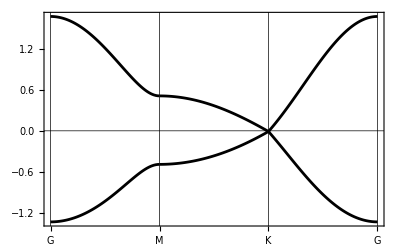

```mathematica
bandplot[
  graphenePath,
  60,
  grapheneHamiltonian,
  {e1 -> 0.05, r1 -> 0.02, t1 -> 0.5}
]
```

The two bands meet at K. plotRange only changes the displayed energy range; it does not change the energies or the position of the crossing.

Multiple orbitals and multiple Wyckoff positions

For several inequivalent Wyckoff positions, list one representative of each in wyckoffposition and place its orbitals in the corresponding entry of basisFunctions. In the CsCl example below, the corner site carries s, and the body-center site carries px, py, and pz. The full Hamiltonian is shown in the order {s,px,py,pz}, including the onsite terms and hopping between the two sites.

```mathematica
csclOperations = msgop[gray[221]];
init[
  lattice -> {
    {a, 0, 0},
    {0, a, 0},
    {0, 0, a}
  },
  lattpar -> {a -> 1},
  wyckoffposition -> {
    {{0, 0, 0}, {0, 0, 0}},
    {{1/2, 1/2, 1/2}, {0, 0, 0}}
  },
  symminformation -> csclOperations,
  basisFunctions -> {{"s"}, {"px", "py", "pz"}}
];
csclHamiltonian = Sum[symham[i], {i, 2}];
validationBandPath = {
  {{{0, 0, 0}, {1/2, 0, 0}}, {"G", "X"}},
  {{{1/2, 0, 0}, {1/2, 1/2, 0}}, {"X", "M"}},
  {{{1/2, 1/2, 0}, {0, 0, 0}}, {"M", "G"}}
};
```

```mathematica
orbitalTable[]
```

Hamiltonian dimension = 4; representation mode = DirectProduct |  |  |  |  |  |  |  |  |  |  | 
H index | Site | Wyckoff orbit | Atom | Fractional position | Cartesian position | Local orbital | Input basis | Actual basis state | Spin structure | Spin state | Transport operation
1 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 1 | s | 1 | Spinless | None | None
2 | 2 | 2 | 1 | {1/2,1/2,1/2} | {1/2,1/2,1/2} | 1 | px | x | Spinless | None | None
3 | 2 | 2 | 1 | {1/2,1/2,1/2} | {1/2,1/2,1/2} | 2 | py | y | Spinless | None | None
4 | 2 | 2 | 1 | {1/2,1/2,1/2} | {1/2,1/2,1/2} | 3 | pz | z | Spinless | None | None

```mathematica
csclHamiltonian = FullSimplify[ExpToTrig[csclHamiltonian]];
MatrixForm[csclHamiltonian]
```

(e1 | -8 ⅈ t1 Cos[ky/2] Cos[kz/2] Sin[kx/2] | -8 ⅈ t1 Cos[kx/2] Cos[kz/2] Sin[ky/2] | -8 ⅈ t1 Cos[kx/2] Cos[ky/2] Sin[kz/2]
8 ⅈ t1 Cos[ky/2] Cos[kz/2] Sin[kx/2] | e2 | 0 | 0
8 ⅈ t1 Cos[kx/2] Cos[kz/2] Sin[ky/2] | 0 | e2 | 0
8 ⅈ t1 Cos[kx/2] Cos[ky/2] Sin[kz/2] | 0 | 0 | e2)

```mathematica
bandManipulate[validationBandPath, 30, csclHamiltonian]
```

A spinful antiunitary model

A spin-space group allows the spin rotation to be specified separately from the spatial operation. The following example has a pure spin C4 rotation and a half translation combined with time reversal. In each dictionary entry, spin -> {S,0} denotes a unitary operation and spin -> {S,1} an antiunitary one; S is the spin-rotation matrix.

```mathematica
identity3 = IdentityMatrix[3];
c4z = {{0, -1, 0}, {1, 0, 0}, {0, 0, 1}};
collinearSSG = <|
  "C4spin" -> <|
    "space" -> {identity3, {0, 0, 0}},
    "spin" -> {c4z, 0}
  |>,
  "tauHalfT" -> <|
    "space" -> {identity3, {1/2, 0, 0}},
    "spin" -> {identity3, 1}
  |>
|>;
init[
  lattice -> {{a, 0, 0}, {0, a, 0}, {0, 0, a}},
  lattpar -> {a -> 1},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 1}}},
  symminformation -> collinearSSG,
  basisFunctions -> {{"sup", "sdn"}},
  GenerateSymmetryGroup -> True
];
collinearHamiltonian = Sum[symham[i], {i, 2}];
validationBandPath = {
  {{{0, 0, 0}, {1/2, 0, 0}}, {"G", "X"}},
  {{{1/2, 0, 0}, {1/2, 1/2, 0}}, {"X", "M"}},
  {{{1/2, 1/2, 0}, {0, 0, 0}}, {"M", "G"}}
};
```

Use atompos again to view the two atoms and their magnetization directions:

```mathematica
atompos
```

{{{{0,0,0},{0,0,1}},{{1/2,0,0},{0,0,-1}}}}

The moments at {0,0,0} and {1/2,0,0} point along +z and -z. Use showCrystalStructure to draw the atoms and their opposite moments:

```mathematica
showCrystalStructure[]
```

-Graphics3D-

```mathematica
MatrixForm[collinearHamiltonian]
```

(e2 | 0 | ⅇ^(-(ⅈ kx)/2) (t1+ⅈ t3)+ⅇ^((ⅈ kx)/2) (t2+ⅈ t4) | 0
0 | e1 | 0 | ⅇ^((ⅈ kx)/2) (t1+ⅈ t3)+ⅇ^(-(ⅈ kx)/2) (t2+ⅈ t4)
ⅇ^((ⅈ kx)/2) (t1-ⅈ t3)+ⅇ^(-(ⅈ kx)/2) (t2-ⅈ t4) | 0 | e1 | 0
0 | ⅇ^(-(ⅈ kx)/2) (t1-ⅈ t3)+ⅇ^((ⅈ kx)/2) (t2-ⅈ t4) | 0 | e2)

```mathematica
showSymmetryRepresentations[]
```

Representation mode: DirectProduct; dimension = 4; showing 3 of 8 operations |  |  |  |  |  |  | 
Index | Label | Generator | R | t | SpinAction | Type | Matrix
2 | GeneratedSSG2 | Yes | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | {0,0,0} | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | Unitary | (-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)
3 | C4spin | Yes | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | {0,0,0} | (0 | -1 | 0
1 | 0 | 0
0 | 0 | 1) | Unitary | ((1-ⅈ)/(√2) | 0 | 0 | 0
0 | (1+ⅈ)/(√2) | 0 | 0
0 | 0 | (1-ⅈ)/(√2) | 0
0 | 0 | 0 | (1+ⅈ)/(√2))
5 | GeneratedSSG5 | Yes | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | {1/2,0,0} | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | Antiunitary | (0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

```mathematica
bandManipulate[validationBandPath, 30, collinearHamiltonian]
```

DirectProduct uses the symmetry action on the orbitals supplied at each site. Induced starts from local states at one representative site and generates the symmetry-related states. For example, in the cubic p-orbital model, DirectProduct requires px, py, and pz explicitly, whereas Induced can start from px at the representative site. The operation relating two sites may also include time reversal.

Related functions and tutorials

init ▪ symham ▪ orbitalTable ▪ showbonds ▪ bandManipulate ▪ General Examples

History